Parts of this notebook are based on a notebook downloaded from http://mathworld.wolfram.com/notebooks/Curves/Parabola.nb 
by Eric Weisstein

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Parabola.html.

#### Envelope of Tangents:

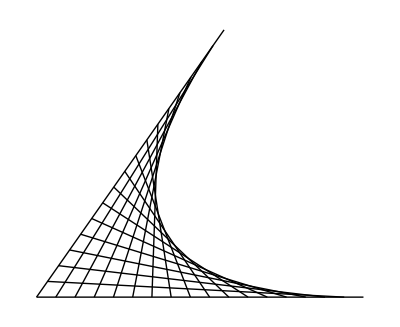

```mathematica
ParabolaStrings[a_,n_]:=Module[{i},
		Graphics[{
				Line[{{0,0},{1,0}}],Line[{{0,0},{Cos[a],Sin[a]}}],
				Table[Line[{{i/n,0},(1-i/n){Cos[a],Sin[a]}}],{i,n-1}]
				}]
]

ParabolaStringsPoints[a_,n_]:=Module[{i},
		Graphics[{
				ParabolaStrings[a,n][[1]],
{PointSize[.03],
				Point/@Table[{i/n,0},{i,n-1}],
				Point/@Table[(1-i/n){Cos[a],Sin[a]},{i,n-1}]
					}
			}]
	]

Final=Show[ParabolaStrings[55Degree,17],
				AspectRatio->Automatic]
```

```mathematica
Export["envelope.pdf",Final];
```

#### A Parabola defined by a point and a line:

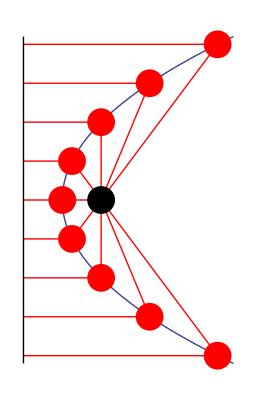

```mathematica
Parabola[a_,n_]:=Module[{dy=.1},Show[Graphics[{{RGBColor[1,0,0],Table[Line[{{-a,t},{t^2/4/a,t},{a,0}}],{t,-2,2,2/n}]},
ParametricPlot[{t^2/4/a, t},{t,-2-dy,2+dy},Ticks->None,DisplayFunction->Identity][[1]],
PointSize[.05],Point[{a,0}],
Line[{{-a,-2-dy},{-a,2+dy}}],
{RGBColor[1,0,0],Table[Point[{t^2/4/a,t}],{t,-2,2,2/n}]}
},AspectRatio->Automatic,DisplayFunction->Identity]
]
]
Final=Show[Parabola[.5,4],DisplayFunction->$DisplayFunction]
```

```mathematica
Export["parabolapointline.pdf",Final];
```

#### Some lines and a parabola

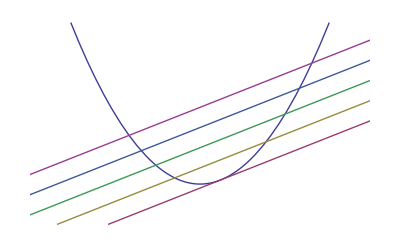

```mathematica
Plot[{x^2,2x-1,2x+4,2x+9,2x+14,2x+19},{x,-10,10},Axes->False,PlotRange->{{-8,8},{-10,40}}]
```

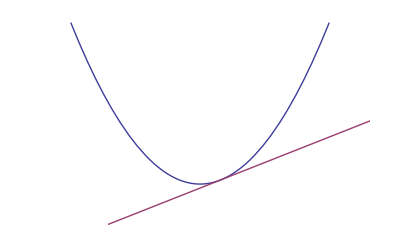

```mathematica
Plot[{x^2,2x-1},{x,-10,10},Axes->False,PlotRange->{{-8,8},{-10,40}}]
```

#### Conic Sections

```mathematica
one=Graphics3D[{Gray,Opacity[.60],Specularity[White,20],Lighting->"Neutral",Cone[]}];
three = ParametricPlot3D[{0,1,2}t+{1,0,0}s,{t,-1,.65},{s,-1,1},PlotPoints->{5,5},PlotStyle->{Opacity[.75],GrayLevel[1],Specularity[White,20],Lighting->"Neutral"}];
Final=Show[one,three,ViewPoint->{-2.395, -0.605, 2.312},Boxed->False]
```

-Graphics3D-

```mathematica
Export["parabolacone.jpg",Final,ImageResolution->300];
```

#### Analytic Geometry

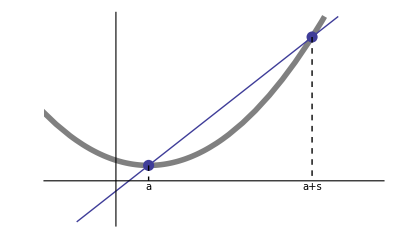

```mathematica
graph1=Plot[1+x^2-x,{x,-5,5},PlotRange->{{-1,4},{-2,8}},Ticks->False,PlotStyle->{{Thickness[0.01],GrayLevel[0.5]}},DisplayFunction->Identity];
graph2=Plot[-.5+2.5x,{x,-5,5},PlotRange->{{-1,4},{-2,8}},Ticks->False,DisplayFunction->Identity];
dot1=ListPlot[{{.5,.75}},PlotStyle->PointSize[0.02],DisplayFunction->Identity];
dot2=ListPlot[{{3,7}},PlotStyle->PointSize[0.02],DisplayFunction->Identity];
linus1=Show[Graphics[{Dashing[{0.01,0.01}],Line[{{.5,.75},{.5,0}}]}],DisplayFunction->Identity];
linus2=Show[Graphics[{Dashing[{0.01,0.01}],Line[{{3,7},{3,0}}]}],DisplayFunction->Identity];
words=Show[Graphics[{Text[StyleForm["a",FontFamily->"Times",FontSize->10,FontSlant->"Italic"],{.5,-.3}],Text[StyleForm["a+s",FontFamily->"Times",FontSize->10,FontSlant->"Italic"],{3,-.3}]}],DisplayFunction->Identity];
Show[graph1,graph2,dot1,dot2,linus1,linus2,words,DisplayFunction->$DisplayFunction]
```